# Orbit

## Definitions

```mathematica
horizontalQ[a_Integer, b_Integer, ts_List]:=Block[{result=True},
	Do[
		If[ts[[x]] < ts[[a]] && ts[[x]] < ts[[b]],result=True,result=False;Return[False]],
		{x,a+1,b-1}
	];
	Return[result]
]
```

```mathematica
visibleQ[a_Integer, b_Integer, ts_List]:=Block[{result=True},
	Do[
		If[ts[[x]] >= ts[[a]]+(ts[[b]]−ts[[a]])(x−a)/(b−a),result=False;Return[]],
		{x,a+1,b-1}
	];
	result
]
```

```mathematica
naturalVisibility[series_]:=Block[{visibles},
	visibles={};
	Do[
		Do[
			If[visibleQ[i,j,series],AppendTo[visibles,i->j],Null],
			{j,i+1,Length@series}
		],
		{i,1,Length@series-1}
	];
	Return[visibles]
]
```

```mathematica
horizontalVisibility[series_]:=Block[{visibles},
	visibles={};
	Do[
		Do[
			If[horizontalQ[i,j,series],AppendTo[visibles,i->j],Null],
			{j,i+1,Length@series}
		],
		{i,1,Length@series-1}
	];
	Return[visibles]
]
```

```mathematica
plotModel[count_, len_]:=Block[
{countrel,nlm,x,C,γ},
countrel=Table[{x,Lookup[count,x]/len}, {x,Keys[count]}];
nlm=NonlinearModelFit[countrel,C x^-γ,{C,γ},x];
{
{#1,Differences[#2][[1]]/2}&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]],
Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],
Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
}
]
```

## Divisors graph

```mathematica
divisors=Table[x<->Length@Divisors[x],{x,2,100003}];
```

```mathematica
graph=Graph[divisors[[;;10000]]];
```

```mathematica
graph
```

```mathematica
Length@divisors
```

100002

```mathematica
orbits=GraphDistance[graph,2];
```

```mathematica
orbits[[1]]=1;
```

```mathematica
maxDist=0;
dist=Table[If[x>maxDist,maxDist=x];maxDist,{x,orbits}];
```

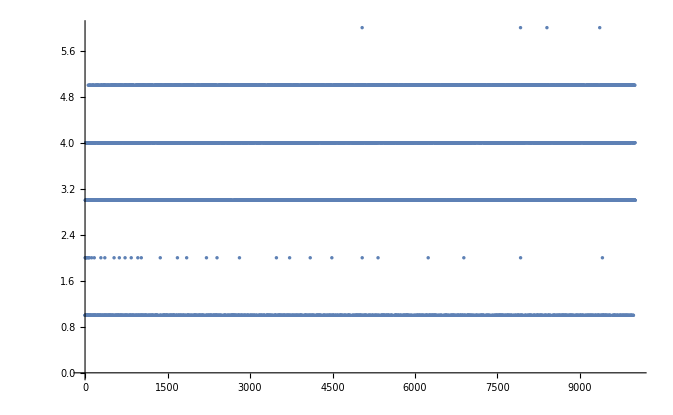

```mathematica
ListPlot[orbits]
```

## Natural Visibility

Fazer grau médio e comparar <l> = log N/log < k >

```mathematica
series=#[[2]]&/@divisors;
```

```mathematica
links=naturalVisibility[series[[;;10000]]];
g=Graph[links];
degrees=Counts[VertexDegree[g]]/Length@VertexDegree[g];
nlm=NonlinearModelFit[Table[{c,Lookup[degrees,c]},{c,Keys[degrees]}],C x^-γ,{γ,C},x];
nlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
γ | 0.637899 | 0.133626 | {0.369634,0.906163}
C | 0.137492 | 0.0324671 | {0.0723111,0.202672}

```mathematica
Mean[VertexDegree[g]]//N
```

5.5962

```mathematica
Log[10000]/Log[Mean[VertexDegree[g]]]//N
```

5.34836

```mathematica
Export[NotebookDirectory[]<>"natural-links.dat",links]
```

/Users/blmayer/doctorate/thesis/article-2/natural-links.dat

```mathematica
Divisors[60]//Length
```

12

```mathematica
Divisors[12]//Length
```

6

```mathematica
Divisors[10000]//Length
```

25

## Horizontal Visibility

```mathematica
linksH=horizontalVisibility[series[[;;10000]]];
gH=Graph[linksH];
degreesH=Counts[VertexDegree[gH]]/Length@VertexDegree[gH];
nlmH=NonlinearModelFit[Table[{c,Lookup[degreesH,c]},{c,Keys[degreesH]}],C x^-γ,{γ,C},x];
nlmH["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
γ | 0.637222 | 0.314564 | {-0.0211672,1.29561}
C | 0.19065 | 0.0834532 | {0.0159808,0.36532}

```mathematica
Mean[VertexDegree[gH]]//N
```

3.5656

```mathematica
Log[10000]/Log[Mean[VertexDegree[gH]]]//N
```

7.24464

```mathematica
Export[NotebookDirectory[]<>"horizontal-links.dat",links]
```

/Users/blmayer/doctorate/thesis/article-2/horizontal-links.dat

## Orbits graph

```mathematica
orbits=GraphDistance[graph,2];
```

This makes the graph connected, and it makes sense: all 2-primes have length 1 now.

```mathematica
orbits[[1]]=1;
```

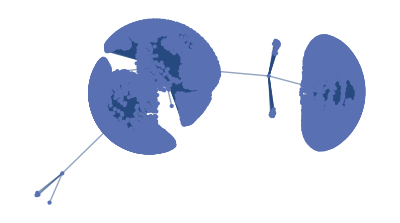

```mathematica
g=Graph[Table[x<->orbits[[x-1]],{x,2,Length@orbits}],VertexLabels->Placed["Name",Tooltip]]
```

```mathematica
orbits2=GraphDistance[graph,2];
```

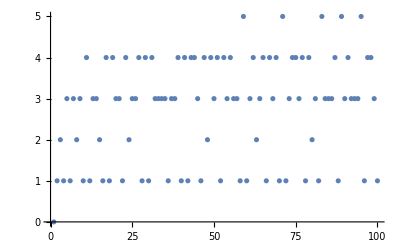

```mathematica
ListPlot[orbits2[[;;100]]]
```

## Natural Visibility

```mathematica
linksO=naturalVisibility[orbits];
gO=Graph[linksO];
degreesO=Counts[VertexDegree[gO]]/Length@VertexDegree[gO];
nlm=NonlinearModelFit[Table[{c,Lookup[degreesO,c]},{c,Keys[degreesO]}],C x^-γ,{γ,C},x];
nlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
γ | 1.31254 | 0.110742 | {1.08446,1.54061}
C | 0.708794 | 0.091918 | {0.519485,0.898102}

```mathematica
Mean[VertexDegree[gO]]//N
```

4.869

```mathematica
Log[10000]/Log[Mean[VertexDegree[gO]]]//N
```

5.81869

```mathematica
Export[NotebookDirectory[]<>"natural-orbit-links.dat",links]
```

/Users/blmayer/doctorate/thesis/article-2/natural-orbit-links.dat

## Horizontal Visibility

```mathematica
linksOH=horizontalVisibility[orbits];
gOH=Graph[linksOH];
degreesOH=Counts[VertexDegree[gOH]]/Length@VertexDegree[gOH];
nlm=NonlinearModelFit[Table[{c,Lookup[degreesOH,c]},{c,Keys[degreesOH]}],C x^-γ,{γ,C},x];
nlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
γ | 0.353266 | 0.638383 | {-1.2088,1.91533}
C | 0.198968 | 0.154959 | {-0.180204,0.57814}

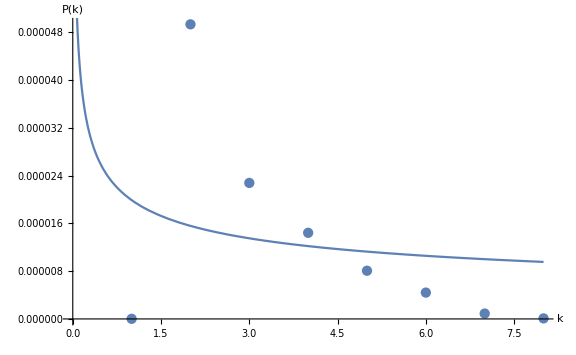
{{{0.0000198968,0.0000379172},{0.353266,1.56207}},-Graphics-}

```mathematica
plotModel[degreesOH,10000]
```

```mathematica
Mean[VertexDegree[gOH]]//N
```

2.9848

```mathematica
Log[10000]/Log[Mean[VertexDegree[gOH]]]//N
```

8.42256

```mathematica
Export[NotebookDirectory[]<>"horizontal-orbit-links.dat",links]
```

/Users/blmayer/doctorate/thesis/article-2/horizontal-orbit-links.dat